```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["../exports/dr7_bal.csv"];
totalData=Import["../exports/dr7_all.csv"];
```

```mathematica
Histogram[
{
totalData[[All,4]],
data[[All,4]]
},10]
```

```mathematica
|
```

```mathematica
(*ListPlot[
{
totalData[[All, {2,3}]],
data[[All, {2,3}]]
},
AxesLabel->{"RA","Dec"}
]*)
```

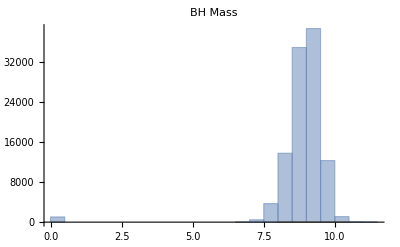

| Mean Mass | Standard Deviation
Normalized Sample | 9.32662 | 0.393716
Full DR7 Sample | 8.87252 | 1.01232

```mathematica
Histogram[
{
data[[All,139]],
totalData[[All,139]]
},
30,
PlotLabel->"BH Mass",
PlotRange->All
]
BHMasses={
{
"",
"Mean Mass",
"Standard Deviation"
},{
"Normalized Sample",
Mean[data[[All,139]]],
StandardDeviation[data[[All, 139]]]
},{
"Full DR7 Sample",
Mean[totalData[[All,139]]],
StandardDeviation[totalData[[All,139]]]
}
};
BHMasses//TableForm
```

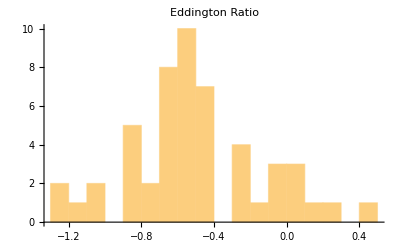

| Mean | Standard Deviation
Normalized Sample | -0.505431 | 0.359858
Full DR7 Sample | -10.5549 | 98.3511

```mathematica
Histogram[data[[All,141]],20, PlotLabel->"Eddington Ratio"]
EddingtonRatios={
{
"",
"Mean",
"Standard Deviation"
},{
"Normalized Sample",
Mean[data[[All,141]]],
StandardDeviation[data[[All, 141]]]
},{
"Full DR7 Sample",
Mean[totalData[[All,141]]],
StandardDeviation[totalData[[All,141]]]
}
};
EddingtonRatios//TableForm
```

```mathematica
meanData=Table[Mean[data[[All,i]]]//N, {i, 2, 142}];
stdDev=Table[StandardDeviation[data[[All,i]]]//N, {i, 2, 142}];
cv=Table[If[meanData[[i]]≠0,stdDev[[i]]/meanData[[i]],"NaN"],{i,1,141}];
labels=Table[i,{i,2,142}];
```

```mathematica
meanTotalData=Table[Mean[totalData[[All,i]]]//N, {i, 2, 142}];
totalStdDev=Table[StandardDeviation[totalData[[All,i]]]//N, {i, 2, 142}];
totalCV=Table[If[meanTotalData[[i]]≠0,totalStdDev[[i]]/meanTotalData[[i]],"NaN"],{i,1,141}];
```

Part::partw: Part 2 of {105763} does not exist.

Part::partw: Part 2 of {105763.} does not exist.

Part::partw: Part 3 of {105763} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of {105763} does not exist.

Part::partw: Part 2 of {105763.} does not exist.

Part::partw: Part 3 of {105763} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
dataTable={labels,meanData,stdDev,cv}//Transpose;
```

```mathematica
totalDataTable={labels,meanTotalData,totalStdDev, totalCV}//Transpose;
```

```mathematica
dataTable//Dimensions
totalDataTable//Dimensions
```

{141,4}

{141,4}

```mathematica
Table[
{
i+1,
dataTable[[i,4]],
totalDataTable[[i,4]]
},
{i,1,141}
];
SortBy[%,#[[2]]&]
```

{{3,-6.24919,If[Mean[{{105763.}}⟦All,3⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{103,-1.42931,If[Mean[{{105763.}}⟦All,103⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{100,-0.868239,If[Mean[{{105763.}}⟦All,100⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{136,-0.714999,If[Mean[{{105763.}}⟦All,136⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{110,-0.713847,If[Mean[{{105763.}}⟦All,110⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{141,-0.711983,If[Mean[{{105763.}}⟦All,141⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{132,-0.581204,If[Mean[{{105763.}}⟦All,132⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{91,-0.554219,If[Mean[{{105763.}}⟦All,91⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{85,-0.54428,If[Mean[{{105763.}}⟦All,85⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{134,-0.52037,If[Mean[{{105763.}}⟦All,134⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{22,-0.518467,If[Mean[{{105763.}}⟦All,22⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{99,-0.466079,If[Mean[{{105763.}}⟦All,99⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{11,-0.0265271,If[Mean[{{105763.}}⟦All,11⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{17,-0.00970234,If[Mean[{{105763.}}⟦All,17⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{20,0.,If[Mean[{{105763.}}⟦All,20⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{26,0.,If[Mean[{{105763.}}⟦All,26⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{28,0.,If[Mean[{{105763.}}⟦All,28⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{30,0.,If[Mean[{{105763.}}⟦All,30⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{32,0.,If[Mean[{{105763.}}⟦All,32⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{34,0.,If[Mean[{{105763.}}⟦All,34⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{36,0.,If[Mean[{{105763.}}⟦All,36⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{38,0.,If[Mean[{{105763.}}⟦All,38⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{40,0.,If[Mean[{{105763.}}⟦All,40⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{42,0.,If[Mean[{{105763.}}⟦All,42⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{44,0.,If[Mean[{{105763.}}⟦All,44⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{46,0.,If[Mean[{{105763.}}⟦All,46⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{48,0.,If[Mean[{{105763.}}⟦All,48⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{50,0.,If[Mean[{{105763.}}⟦All,50⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{51,0.,If[Mean[{{105763.}}⟦All,51⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{52,0.,If[Mean[{{105763.}}⟦All,52⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{55,0.,If[Mean[{{105763.}}⟦All,55⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{57,0.,If[Mean[{{105763.}}⟦All,57⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{59,0.,If[Mean[{{105763.}}⟦All,59⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{61,0.,If[Mean[{{105763.}}⟦All,61⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{63,0.,If[Mean[{{105763.}}⟦All,63⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{65,0.,If[Mean[{{105763.}}⟦All,65⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{67,0.,If[Mean[{{105763.}}⟦All,67⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{70,0.,If[Mean[{{105763.}}⟦All,70⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{72,0.,If[Mean[{{105763.}}⟦All,72⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{74,0.,If[Mean[{{105763.}}⟦All,74⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{76,0.,If[Mean[{{105763.}}⟦All,76⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{78,0.,If[Mean[{{105763.}}⟦All,78⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{79,0.,If[Mean[{{105763.}}⟦All,79⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{80,0.,If[Mean[{{105763.}}⟦All,80⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{83,0.,If[Mean[{{105763.}}⟦All,83⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{115,0.,If[Mean[{{105763.}}⟦All,115⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{116,0.,If[Mean[{{105763.}}⟦All,116⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{117,0.,If[Mean[{{105763.}}⟦All,117⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{118,0.,If[Mean[{{105763.}}⟦All,118⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{119,0.,If[Mean[{{105763.}}⟦All,119⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{120,0.,If[Mean[{{105763.}}⟦All,120⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{121,0.,If[Mean[{{105763.}}⟦All,121⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{122,0.,If[Mean[{{105763.}}⟦All,122⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{128,0.,If[Mean[{{105763.}}⟦All,128⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{130,0.,If[Mean[{{105763.}}⟦All,130⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{112,0.00213534,If[Mean[{{105763.}}⟦All,112⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{12,0.00610453,If[Mean[{{105763.}}⟦All,12⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{23,0.00618106,If[Mean[{{105763.}}⟦All,23⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{104,0.00757602,If[Mean[{{105763.}}⟦All,104⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{7,0.0127017,If[Mean[{{105763.}}⟦All,7⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{137,0.0422142,If[Mean[{{105763.}}⟦All,137⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{139,0.0422142,If[Mean[{{105763.}}⟦All,139⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{4,0.171162,If[Mean[{{105763.}}⟦All,4⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{114,0.232337,If[Mean[{{105763.}}⟦All,114⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{106,0.368112,If[Mean[{{105763.}}⟦All,106⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{123,0.436259,If[Mean[{{105763.}}⟦All,123⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{108,0.460751,If[Mean[{{105763.}}⟦All,108⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{105,0.485638,If[Mean[{{105763.}}⟦All,105⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{13,0.495345,If[Mean[{{105763.}}⟦All,13⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{24,0.495345,If[Mean[{{105763.}}⟦All,24⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{113,0.496427,If[Mean[{{105763.}}⟦All,113⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{109,0.499493,If[Mean[{{105763.}}⟦All,109⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{2,0.501742,If[Mean[{{105763.}}⟦All,2⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{111,0.541092,If[Mean[{{105763.}}⟦All,111⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{6,0.546761,If[Mean[{{105763.}}⟦All,6⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{5,0.638073,If[Mean[{{105763.}}⟦All,5⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{9,0.654081,If[Mean[{{105763.}}⟦All,9⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{138,0.76327,If[Mean[{{105763.}}⟦All,138⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{140,0.76327,If[Mean[{{105763.}}⟦All,140⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{107,0.893286,If[Mean[{{105763.}}⟦All,107⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{126,1.03225,If[Mean[{{105763.}}⟦All,126⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{101,1.42944,If[Mean[{{105763.}}⟦All,101⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{102,1.50341,If[Mean[{{105763.}}⟦All,102⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{125,1.61809,If[Mean[{{105763.}}⟦All,125⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{21,2.18178,If[Mean[{{105763.}}⟦All,21⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{84,2.18185,If[Mean[{{105763.}}⟦All,84⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{90,2.18189,If[Mean[{{105763.}}⟦All,90⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{131,2.19156,If[Mean[{{105763.}}⟦All,131⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{135,2.34455,If[Mean[{{105763.}}⟦All,135⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{88,2.41275,If[Mean[{{105763.}}⟦All,88⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{92,2.41643,If[Mean[{{105763.}}⟦All,92⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{97,2.44064,If[Mean[{{105763.}}⟦All,97⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{94,2.51205,If[Mean[{{105763.}}⟦All,94⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{124,2.58102,If[Mean[{{105763.}}⟦All,124⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{98,2.58635,If[Mean[{{105763.}}⟦All,98⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{14,2.76586,If[Mean[{{105763.}}⟦All,14⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{133,2.76997,If[Mean[{{105763.}}⟦All,133⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{86,3.00088,If[Mean[{{105763.}}⟦All,86⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{89,3.00363,If[Mean[{{105763.}}⟦All,89⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{95,3.01452,If[Mean[{{105763.}}⟦All,95⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{96,3.03759,If[Mean[{{105763.}}⟦All,96⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{87,3.49358,If[Mean[{{105763.}}⟦All,87⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{93,3.79333,If[Mean[{{105763.}}⟦All,93⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{8,4.00876,If[Mean[{{105763.}}⟦All,8⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{15,4.999,If[Mean[{{105763.}}⟦All,15⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{16,5.42244,If[Mean[{{105763.}}⟦All,16⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{18,6.87328,If[Mean[{{105763.}}⟦All,18⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{10,NaN,If[Mean[{{105763.}}⟦All,10⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{19,NaN,If[Mean[{{105763.}}⟦All,19⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{25,NaN,If[Mean[{{105763.}}⟦All,25⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{27,NaN,If[Mean[{{105763.}}⟦All,27⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{29,NaN,If[Mean[{{105763.}}⟦All,29⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{31,NaN,If[Mean[{{105763.}}⟦All,31⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{33,NaN,If[Mean[{{105763.}}⟦All,33⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{35,NaN,If[Mean[{{105763.}}⟦All,35⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{37,NaN,If[Mean[{{105763.}}⟦All,37⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{39,NaN,If[Mean[{{105763.}}⟦All,39⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{41,NaN,If[Mean[{{105763.}}⟦All,41⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{43,NaN,If[Mean[{{105763.}}⟦All,43⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{45,NaN,If[Mean[{{105763.}}⟦All,45⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{47,NaN,If[Mean[{{105763.}}⟦All,47⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{49,NaN,If[Mean[{{105763.}}⟦All,49⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{53,NaN,If[Mean[{{105763.}}⟦All,53⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{54,NaN,If[Mean[{{105763.}}⟦All,54⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{56,NaN,If[Mean[{{105763.}}⟦All,56⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{58,NaN,If[Mean[{{105763.}}⟦All,58⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{60,NaN,If[Mean[{{105763.}}⟦All,60⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{62,NaN,If[Mean[{{105763.}}⟦All,62⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{64,NaN,If[Mean[{{105763.}}⟦All,64⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{66,NaN,If[Mean[{{105763.}}⟦All,66⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{68,NaN,If[Mean[{{105763.}}⟦All,68⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{69,NaN,If[Mean[{{105763.}}⟦All,69⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{71,NaN,If[Mean[{{105763.}}⟦All,71⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{73,NaN,If[Mean[{{105763.}}⟦All,73⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{75,NaN,If[Mean[{{105763.}}⟦All,75⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{77,NaN,If[Mean[{{105763.}}⟦All,77⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{81,NaN,If[Mean[{{105763.}}⟦All,81⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{82,NaN,If[Mean[{{105763.}}⟦All,82⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{127,NaN,If[Mean[{{105763.}}⟦All,127⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{129,NaN,If[Mean[{{105763.}}⟦All,129⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]},{142,NaN,If[Mean[{{105763.}}⟦All,142⟧]≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN]}}

```mathematica
totalCV
```

{0.392507,0.807336,0.53414,0.525666,0.578509,0.0152352,2.54812,0.332696,0.88154,-0.0527525,0.0333229,5.79092,4.18773,9.85063,13.3225,-0.0336361,14.0628,1.89238,-0.595781,0.482728,-2.2202,1.0089,-1.0503,4.57844,-0.230228,5.54648,10.3982,5.25518,246.039,4.67138,-0.31966,5.40968,7.54061,8.52045,-5.63113,4.72374,-0.345473,7.08611,244.305,5.04336,-0.280337,8.38032,-5.46047,5.06776,-0.280515,9.7177,298.847,11.992,-6.58721,-0.218502,-0.367053,4.24073,4.91479,-0.736554,1.91242,-0.614188,2.35402,3.41175,14.5521,If[9.45331×10^-6 (7.60741×10^20+19. Infinity)≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN],2.0647,-0.984283,2.37932,2.87002,5.14356,If[9.45331×10^-6 (4.35887×10^19+20. Infinity)≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN],2.24156,2.01941,-0.696141,5.63031,If[9.45331×10^-6 (1.44113×10^21+9. Infinity)≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN],2.01993,-0.588231,3.88483,If[9.45331×10^-6 (4.00388×10^27+6. Infinity)≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN],5.68166,If[9.45331×10^-6 (4.07567×10^19+19. )≠0,totalStdDev⟦i⟧/meanTotalData⟦i⟧,NaN],-0.528764,-0.924422,1.84968,2.34049,60.3933,0.485301,-2.75067,0.735936,1.44347,11.166,213.201,0.487,-2.85719,0.712722,1.37513,10.4853,324.854,0.646297,1.07212,2.03398,-2.05847,-7.89432,0.459282,0.797385,16.5332,1.01331,-1.15646,1.21332,1.88421,1.51634,139.021,-0.989919,-2.28059,0.941479,1.21238,27.8026,0.218403,16.8969,0.217809,10.2532,0.522929,16.267,0.528707,3.6908,2.02543,1.20429,0.983865,1.88902,1.92315,-0.568061,1.93179,-0.682828,0.49362,-2.89039,0.521595,-5.59502,0.496639,-11.232,1.04605,-1.3641,0.114096,1.39212,-9.31804,11.056}